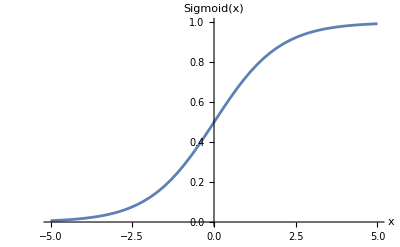

```mathematica
Sigmoid[x_]:=1/(1+Exp[-x])
Plot[Sigmoid[x],{x,-5,5},AxesLabel->{"x","Sigmoid(x)"},PlotRange->{0,1}]
```

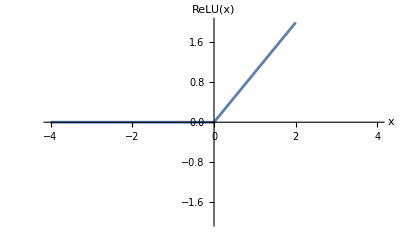

```mathematica
Plot[Max[0,x],{x,-4,4},AxesLabel->{"x","ReLU(x)"},PlotRange->{-2,2}]
```

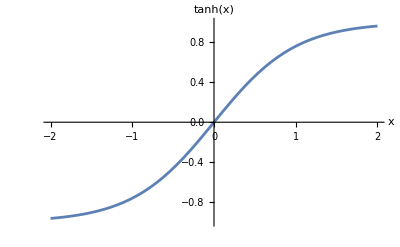

```mathematica
Plot[Tanh[x],{x,-2,2},AxesLabel->{"x","tanh(x)"},PlotRange->{-1,1}]
```

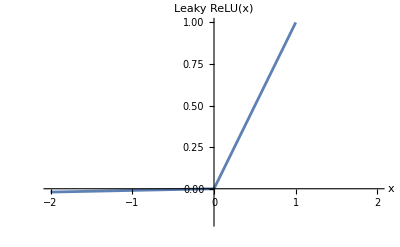

```mathematica
Plot[Piecewise[{{x,x>0},{0.01 x,x<=0}}],{x,-2,2},AxesLabel->{"x","Leaky ReLU(x)"},PlotRange->{-0.2,1}]
```

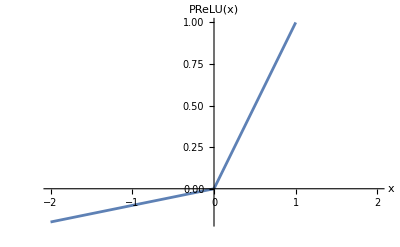

```mathematica
alpha=0.1;  (*You can adjust the alpha value as needed*)
Plot[Piecewise[{{x,x>0},{alpha x,x<=0}}],{x,-2,2},AxesLabel->{"x","PReLU(x)"},PlotRange->{-0.2,1}]
```

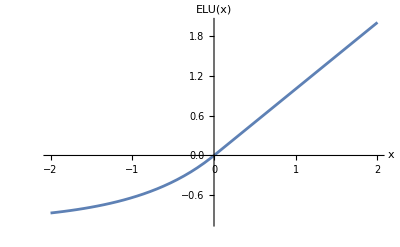

```mathematica
alpha=1;  (*You can adjust the alpha value as needed*)
Plot[Piecewise[{{x,x>0},{alpha (Exp[x]-1),x<=0}}],{x,-2,2},AxesLabel->{"x","ELU(x)"},PlotRange->{-1,2}]
```